Άσκηση 7.1-1

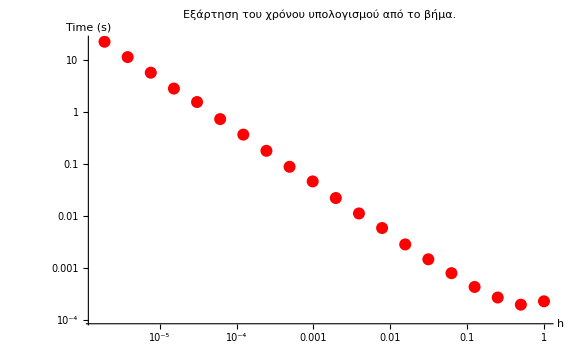
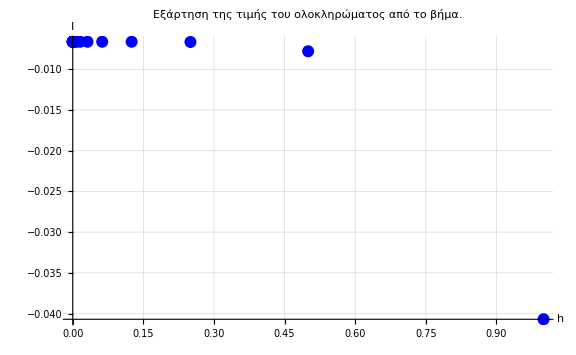
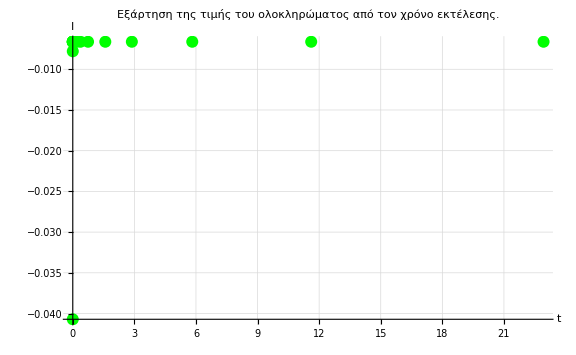
| βήμα (h) | χρόνος | αποτέλεσμα
1 | 1. | 0.000231235 | -0.0407072
2 | 0.5 | 0.000199236 | -0.00778923
3 | 0.25 | 0.000273497 | -0.00664847
4 | 0.125 | 0.000437113 | -0.00662127
5 | 0.0625 | 0.000804794 | -0.00661915
6 | 0.03125 | 0.00148763 | -0.00661883
7 | 0.015625 | 0.00287806 | -0.00661877
8 | 0.0078125 | 0.00595294 | -0.00661875
9 | 0.00390625 | 0.0113631 | -0.00661875
10 | 0.00195313 | 0.0224926 | -0.00661875
11 | 0.000976563 | 0.0469715 | -0.00661875
12 | 0.000488281 | 0.0898188 | -0.00661875
13 | 0.000244141 | 0.18224 | -0.00661875
14 | 0.00012207 | 0.373622 | -0.00661875
15 | 0.0000610352 | 0.74387 | -0.00661875
16 | 0.0000305176 | 1.58458 | -0.00661875
17 | 0.0000152588 | 2.87756 | -0.00661875
18 | 7.62939×10^-6 | 5.81988 | -0.00661875
19 | 3.8147×10^-6 | 11.6129 | -0.00661875
20 | 1.90735×10^-6 | 22.9296 | -0.00661875
 
-Graphics-
 
-Graphics-
-Graphics-

```mathematica
ClearAll["Global`*"]
f[x_]:=(x^2 Cos[5x])/(1+ⅇ^(2x))
(* Ορίζουμε συνάρτηση που υπολογίζει το ορισμένο ολοκλήρωμα συνάρτησης σε συγκεκριμένο διάστημα. *)
integrateTrapezoid[f_,xmin_,xmax_,h_]:=Module[
{ff,sum,i,n=(xmax-xmin)/h},
(* μετατροπή της συνάρτησης σε pure function *)
ff=(Evaluate[f/.x->#])&;
(* υπολογίζουμε τον πρώτο και τον τελευταίο όρο του αθροίσματος *)
sum=N[(ff[xmin]+ff[xmax])/2];
(* υπολογίζουμε τους ενδιάμεσους όρους *)
For[i=1,i<n,i++,
sum=sum+N@ff[xmin+i h];
];
(* δίνουμε το τελικό αποτέλεσμα *)
h sum
];
(* Εκτελούμε για διάφορες τιμές του h και συλλέγουμε τα αποτελέσματα. *)
xmin=0;xmax=5;
results=Reap[
For[h=1.,h>10^-6,h=h/2,
Sow[Flatten@{h,AbsoluteTiming[integrateTrapezoid[f[x],xmin,xmax,h]]}];
]
][[2,1]];
(* Παρουσιάζουμε τα δεδομένα *)
Column[{
TableForm[Map[FullForm,results,{2}],
TableAlignments->{Center, Center},
TableHeadings->{Range[Length[results]],{"βήμα (h)","χρόνος","αποτέλεσμα"}}
],
" ",
ListLogLogPlot[
results[[All,1;;2]],
PlotStyle->{Red,PointSize[0.015]},
AxesLabel->{Style["h",{Bold,12}],Style["Time (s)",{Bold,12}]},
ImageSize->Large,
GridLines->Automatic,
PlotLabel->Style["Εξάρτηση του χρόνου υπολογισμού από το βήμα.",{Bold,15}]
],
" ",
ListPlot[
results[[All,{1,3}]],
PlotRange->All,
AxesOrigin->{0,Min[results[[All,3]]]},
PlotStyle->{Blue,PointSize[0.015]},
AxesLabel->{Style["h",{Bold,12}],Style["I",{Bold,12}]},
ImageSize->Large,
GridLines->Automatic,
PlotLabel->Style["Εξάρτηση της τιμής του ολοκληρώματος από το βήμα.",{Bold,15}]
],
ListPlot[
results[[All,{2,3}]],
PlotRange->All,
AxesOrigin->{0,Min[results[[All,3]]]},
PlotStyle->{Green,PointSize[0.015]},
AxesLabel->{Style["t",{Bold,12}],Style["I",{Bold,12}]},
ImageSize->Large,
GridLines->Automatic,
PlotLabel->Style["Εξάρτηση της τιμής του ολοκληρώματος από τον χρόνο εκτέλεσης.",{Bold,15}]
]
}]
```

Άσκηση 7.3.2-1

E[λ_1 g_1(x)+λ_2 g_2(x)] | = | ∫_(-∞)^∞ [λ_1 g_1(x)+λ_2 g_2(x)]ⅆx
  | = | ∫_(-∞)^∞ λ_1 g_1(x)ⅆx+∫_(-∞)^∞ λ_2 g_2(x)ⅆx
  | = | (λ_1∫)_(-∞)^∞g_1(x)ⅆx+λ_2∫_(-∞)^∞ g_2(x)ⅆx
  | = | λ_1 E[g_1(x)]+λ_2 E[g_2(x)]

var[λ_1 g_1(x)+λ_2 g_2(x)] | = | <[λ_1 g_1(x)+λ_2 g_2(x)]^2>-<λ_1 g_1(x)+λ_2 g_2(x)>^2
  | = | <λ_1^2 g_1^2(x)+λ_2^2 g_2^2(x)+2 λ_1 λ_2 g_1(x)g_2(x)>
-[λ_1<g_1(x)>+λ_2<g_2(x)>]^2
  | = | λ_1^2<g_1^2(x)>+λ_2^2<g_2^2(x)>+2 λ_1 λ_2<g_1(x)g_2(x)>
-λ_1^2<g_1(x)>^2-λ_2^2<g_2(x)>^2-λ_1 λ_2<g_1(x)><g_2(x)>
  | = | λ_1^2(<g_1^2(x)>-<g_1(x)>^2)+λ_2^2(<g_2^2(x)>-<g_2(x)>^2)
+2 λ_1 λ_2(<g_1(x)g_2(x)>-<g_1(x)><g_2(x)>)
  | = | λ_1^2 var[g_1(x)]+λ_2^2 var[g_2(x)]
+2 λ_1 λ_2(<g_1(x)g_2(x)>-<g_1(x)><g_2(x)>)

Άσκηση 7.3.2-3

∑_(n=0)^∞ P(X=n) | = | ∑_(n=0)^∞ λ^n/(n!)e^-λ
  | = | e^-λ∑_(n=0)^∞ λ^n/(n!)
  | = | e^-λ e^λ
  | = | 1

E[X] | = | ∑_(n=0)^∞ n λ^n/(n!)e^-λ
  | = | ∑_(n=1)^∞ (λ λ^(n-1))/((n-1)!)e^-λ
  | = | λe^-λ∑_(n=1)^∞ λ^(n-1)/((n-1)!)
  | =^(k=n-1) | λe^-λ∑_(k=0)^∞ λ^k/(k!)
  | = | λe^-λ e^λ
  | = | λ

var[X] | = | E[X^2]-μ^2
  | = | ∑_(n=0)^∞ n^2 λ^n/(n!)e^-λ-λ^2
  | = | λⅇ^-λ∑_(n=1)^∞ n λ^(n-1)/((n-1)!)e^-λ-λ^2
  | = | λⅇ^-λ∑_(n=1)^∞ (n-1+1)λ^(n-1)/((n-1)!)e^-λ-λ^2
  | = | λⅇ^-λ(∑_(n=1)^∞ (n-1)λ^(n-1)/((n-1)!)e^-λ+∑_(n=1)^∞ λ^(n-1)/((n-1)!)e^-λ)-λ^2
  | = | λⅇ^-λ((λ∑)_(n=2)^∞λ^(n-2)/((n-2)!)e^-λ+∑_(n=1)^∞ λ^(n-1)/((n-1)!)e^-λ)-λ^2
  | =^(k = n-2
m = n-1) | λⅇ^-λ(λⅇ^λ+ⅇ^λ)-λ^2
  | = | λ

Άσκηση 7.3.2-5

E[X] | = | ∫_(-∞)^∞ xf(x)ⅆx
  | = | (∫x)_a^b 1/(b-a)ⅆx
  | = | [1/2 x^2/(b-a)]_a^b
  | = | 1/2(b^2-a^2)/(b-a)
  | = | 1/2(b+a)

var[X] | = | E[X^2]-E[X]^2
  | = | (∫x^2)_a^b 1/(b-a)ⅆx-1/4(b+a)^2
  | = | [1/3 x^3/(b-a)]_a^b-1/4(b+a)^2
  | = | 1/3(a^2+a b+b^2)-1/4(a^2+a b+b^2)
  | = | 1/12(b-a)^2

Άσκηση 7.3.2-6

E[X} | = | ∫_(-∞)^∞ x 1/(σ √(2π))exp[-(x-μ)^2/(2 σ^2)]ⅆx
  | = | 1/(σ √(2π))∫_(-∞)^∞ x exp[-(x-μ)^2/(2 σ^2)]ⅆx
  | =^(y=(χ-μ)/σ) | y∫_(-∞)^∞ (x-μ+μ) exp[-y^2/2]ⅆx
  | = | y∫_(-∞)^∞ (x-μ) exp[-y^2/2]ⅆx+1/(σ √(2π))∫_(-∞)^∞ μ exp[-(x-μ)^2/(2 σ^2)]ⅆx
  | = | -σ^2y∫_(-∞)^∞ -(x-μ)/σ^2exp[-y^2/2]ⅆx+1/(σ √(2π))∫_(-∞)^∞ μ exp[-(x-μ)^2/(2 σ^2)]ⅆx
  | = | [-σ^2exp[-y^2/2]]_0^∞+μ
  | = | 0

var[X] | = | E[(X-E[X])^2]
  | = | ∫_(-∞)^∞ (x-μ)^2 1/(σ √(2π))exp[-(x-μ)^2/(2 σ^2)]ⅆx
  | =^(y=1/(σ √2)) | ∫_(-∞)^∞ σ^2 2 y^2 1/(σ √(2π))exp[-y^2]σ √2 ⅆy
  | = | (2 σ^2)/(√π)(∫_(-∞)^∞ [y(-1/2)ⅇ^(-y^2)]_(-∞)^∞+∫_(-∞)^∞ 1/2 ⅇ^(-y^2)ⅆy)
  | = | (2 σ^2)/(√π)1/2 √π
  | = | σ^2

Άσκηση 7.3.2-9

Ε[Χ] | = | ∫_(-∞)^∞ x f(x)ⅆx
  | = | ∫_0^∞ x λⅇ^-λx ⅆx
  | = | [x ⅇ^-λx]_0^∞-∫_0^∞ ⅇ^-λx ⅆx
  | = | 0-(1/-λ[ⅇ^-λx])_0^∞
  | = | 1/λ

var[X] | = | (E[X^2]-E[X})^2
  | = | ∫_0^∞ x^2 λⅇ^-λx ⅆx-1/λ^2
  | = | [x^2 λ(-1/λ)ⅇ^-λx]_0^∞-∫_0^∞ 2x ⅇ^-λx ⅆx-1/λ^2
  | = | -[2x ⅇ^-λx]_0^∞+∫_0^∞ 2 1/λ ⅇ^-λx ⅆx-1/λ^2
  | = | [2/λ^2 ⅇ^-λx]_0^∞-1/λ^2
  | = | 2/λ^2-1/λ^2
  | = | 1/λ^2